## Fast variable Phase Plate for MINFLUX excitation

### Definitions, optical elements as Jones matrices

```mathematica
waveplateW[ϕ_,θ_]:=Exp[-ⅈ ϕ/2]{{Cos[θ]^2+Exp[ⅈ ϕ]*Sin[θ]^2, (1-Exp[ⅈ ϕ]) Cos[θ]Sin[θ]},{(1-Exp[ⅈ ϕ])Cos[θ] Sin[θ], Sin[θ]^2+Exp[ⅈ ϕ]*Cos[θ]^2}}
waveplate[ϕ_,θ_]:={{Cos[θ]^2+Exp[ⅈ ϕ]*Sin[θ]^2, (1-Exp[ⅈ ϕ]) Cos[θ]Sin[θ]},{(1-Exp[ⅈ ϕ])Cos[θ] Sin[θ], Sin[θ]^2+Exp[ⅈ ϕ]*Cos[θ]^2}} (*global phase removed, now the same as HWP etc.*)
polarizer[θ_]:={{Cos[θ]^2, Cos[θ]Sin[θ]},{Cos[θ]Sin[θ],Sin[θ]^2}}
addphase[ϕ_]:= Exp[ⅈ ϕ]
QWP[θ_]:= waveplate[π/2,θ]
HWP[θ_]:= waveplate[π,θ]
linear[θ_]:=HWP[θ/2].{{1},{0}}
```

#### Simple setup

```mathematica
vin=linear[π/4]//Simplify
pos1=waveplate[ϕ,0].vin//Simplify (*EOM*)
prot=addphase[-ξ/2]HWP[π/4].pos1 //Simplify; (*SLM + lat phase*)
pnr=addphase[ξ/2]pos1//Simplify; (*lat phase*)
outs=polarizer[0].(pnr+prot)//Simplify (*polarizer*)
intout=FullSimplify[Norm[outs]^2,{ξ,ϕ}∈Reals]
```

{{1/(√2)},{1/(√2)}}

{{1/(√2)},{ⅇ^(ⅈ ϕ)/(√2)}}

{{(ⅇ^(-(ⅈ ξ)/2) (ⅇ^(ⅈ ξ)+ⅇ^(ⅈ ϕ)))/(√2)},{0}}

1+Cos[ξ-ϕ]

```mathematica
prot/.ξ->0
pnr/.ξ->0
outs[[1]]/.ξ->0
intout/.ξ->0
```

{{ⅇ^(ⅈ ϕ)/(√2)},{1/(√2)}}

{{1/(√2)},{ⅇ^(ⅈ ϕ)/(√2)}}

{(1+ⅇ^(ⅈ ϕ))/(√2)}

1+Cos[ϕ]

#### Imperfect SLM

```mathematica
pos1=waveplate[ϕ,0].linear[π/4]; (*EOM*)
pos2=HWP[α].pos1; (*compensating HWP*)
prot=addphase[-ξ/2]waveplate[cp π,ρ].pos2 //Simplify; (*SLM + lat phase*)
pnr=addphase[ξ/2]pos2//Simplify; (*lat phase*)
outs=Simplify[polarizer[0].(pnr+prot),{ξ,ϕ,ρ,α,cp}∈Reals];(*polarizer*)
intout=FullSimplify[Norm[outs]^2/.ξ->0,{ξ,ϕ,ρ,α,cp}∈Reals];
```

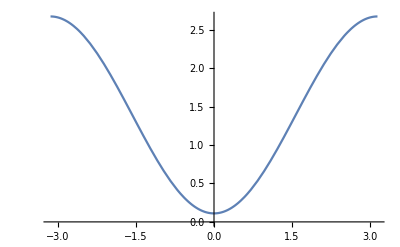

```mathematica
ρb=33.5/180 π;
Plot[intout/.ρ->ρb/.α->0/.cp->1,{ϕ,-π,π}]
```

```mathematica
intout/.ρ->π/4/.α->0/.cp->1//FullSimplify
HWP[0]
```

1-Cos[ϕ]

{{1,0},{0,-1}}

```mathematica
settings={cp->cx,ρ->ρbx};
so:=Minimize[{Abs[intout]}/.settings ,{α,ϕ}]
s:=FindMinimum[{Abs[intout],-π/4<α<π/4,-π/2-0.5<ϕ<π/2+.5}/.settings ,{{α,0},{ϕ,0}},WorkingPrecision->30]
```

FindMinimum::precw: The precision of the argument function (1/8 «1» Abs[(0.765471 ⅇ^(ⅈ ϕ) Sin[0.392755+Times[«2»]]+Sin[0.78551-2 α]+Sin[2 α]-(0.707186-0.707027 ⅈ) (Power[«2»] Plus[«2»]-Sin[«1»]+3 Sin[«1»])) ((-1.2073+«19» ⅈ) («1» «1»-«1»)+«1»)]) is less than WorkingPrecision (30.).

FindMinimum::precw: The precision of the argument function ({{-2.0708<ϕ,-π/4<α,α<π/4,ϕ<2.0708}}) is less than WorkingPrecision (30.).

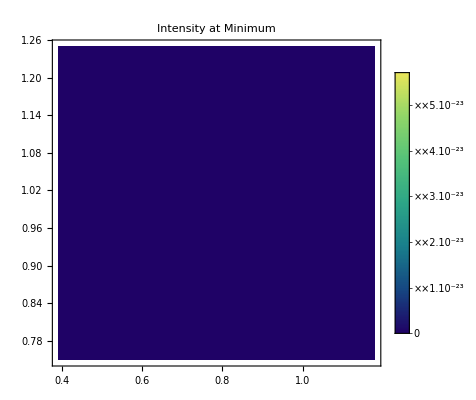

FindMinimum::precw: The precision of the argument function (1/8 «1» Abs[(0.765471 ⅇ^(ⅈ ϕ) Sin[0.392755+Times[«2»]]+Sin[0.78551-2 α]+Sin[2 α]-(0.707186-0.707027 ⅈ) (Power[«2»] Plus[«2»]-Sin[«1»]+3 Sin[«1»])) ((-1.2073+«19» ⅈ) («1» «1»-«1»)+«1»)]) is less than WorkingPrecision (30.).

FindMinimum::precw: The precision of the argument function ({{-2.0708<ϕ,-π/4<α,α<π/4,ϕ<2.0708}}) is less than WorkingPrecision (30.).

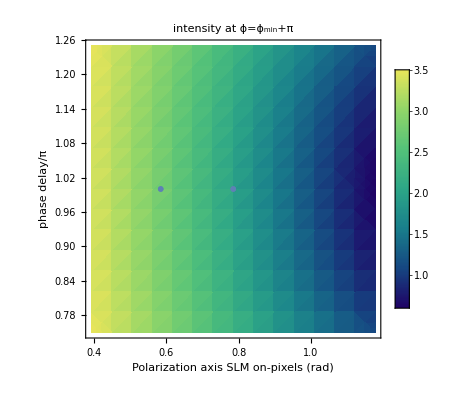

```mathematica
pminint=DensityPlot[s[[1]],{ρbx,π/8,π/2-π/8},{cx,0.75,1.25},PlotLegends->Automatic,PlotRange->All,ColorFunction->"BlueGreenYellow",PlotLabel->"Intensity at Minimum",PerformanceGoal->"Quality"]
p1=DensityPlot[intout/.ϕ-> ϕ-π/.s[[2]]/.settings,{ρbx,π/8,π/2-π/8},{cx,0.75,1.25},PlotLegends->Automatic,ColorFunction->"BlueGreenYellow",PlotRange->{-2,4},AxesLabel->{"Polarization axis SLM on-pixels (rad)","phase delay/π "},PlotLabel->"intensity at ϕ=ϕ_min+π"];
p2=ListPlot[{{π/4,1}},PlotMarkers->o];
p3=ListPlot[{{ρb,1}},PlotMarkers->x];
Show[p1,p2,p3]
```

```mathematica
Export["/Users/ries/Library/Mobile Documents/com~apple~CloudDocs/mEMBL/Projects/MINFLUX/MINFLUXexcitation/paper/Figures/SLMIMin.eps",pminint,"EPS"]
```

/Users/ries/Library/Mobile Documents/com~apple~CloudDocs/mEMBL/Projects/MINFLUX/MINFLUXexcitation/paper/Figures/SLMIMin.eps

```mathematica
Export["/Users/ries/Documents/Figures/SLMImin.eps",pminint,"EPS"]
```

/Users/ries/Documents/Figures/SLMImin.eps

FindMinimum::precw: The precision of the argument function (1/8 «1» Abs[(0.765471 ⅇ^(ⅈ ϕ) Sin[0.392755+Times[«2»]]+Sin[0.78551-2 α]+Sin[2 α]-(0.707186-0.707027 ⅈ) (Power[«2»] Plus[«2»]-Sin[«1»]+3 Sin[«1»])) ((-1.2073+«19» ⅈ) («1» «1»-«1»)+«1»)]) is less than WorkingPrecision (30.).

FindMinimum::precw: The precision of the argument function ({{-2.0708<ϕ,-π/4<α,α<π/4,ϕ<2.0708}}) is less than WorkingPrecision (30.).

FindMinimum::precw: The precision of the argument function (1/8 «1» Abs[(0.765471 ⅇ^(ⅈ ϕ) Sin[0.392755+Times[«2»]]+Sin[0.78551-2 α]+Sin[2 α]-(0.707186-0.707027 ⅈ) (Power[«2»] Plus[«2»]-Sin[«1»]+3 Sin[«1»])) ((-1.2073+«19» ⅈ) («1» «1»-«1»)+«1»)]) is less than WorkingPrecision (30.).

FindMinimum::precw: The precision of the argument function ({{-2.0708<ϕ,-π/4<α,α<π/4,ϕ<2.0708}}) is less than WorkingPrecision (30.).

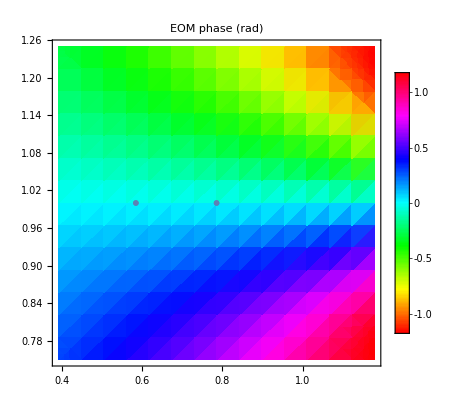

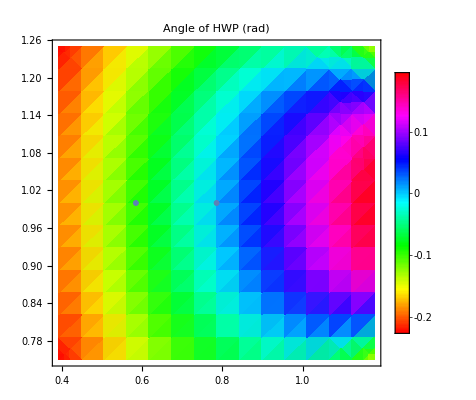

ReplaceAll::reps: {α,ϕ} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ϕ/.{α,ϕ}

```mathematica
pphi=DensityPlot[Mod[ϕ+π,2π]-π/.s[[2]]/.settings,{ρbx,π/8,π/2-π/8},{cx,0.75,1.25},PlotLegends->Automatic,ColorFunction->Hue,PlotRange->All,PlotLabel->"EOM phase (rad)"];
palpha=DensityPlot[Mod[α+π/2,π]-π/2/.s[[2]]/.settings,{ρbx,π/8,π/2-π/8},{cx,0.75,1.25},PlotLegends->Automatic,ColorFunction->Hue,PlotRange->All,PlotLabel->"Angle of HWP (rad)",MaxRecursion->2];
Show[pphi,p2,p3]
Show[palpha,p2,p3]
```

```mathematica
polarizer[0]
```

{{1,0},{0,0}}